# Statistical Measures

## Theme

```mathematica
fontLabels=Directive[FontFamily->"Libertinus Serif",FontSize->22];
fontTicks=Directive[FontFamily->"Libertinus Serif",FontSize->18];

(* https://mathematica.stackexchange.com/questions/54545/is-it-possible-to-define-a-new-plottheme *)
Begin["System`PlotThemeDump`"];
Themes`ThemeRules;(*preload Theme system*)

resolvePlotTheme["myThemeBasic",def:_String]:=Themes`SetWeight[
Join[
{ImageSize->Large},
{LabelStyle->fontLabels},
{TicksStyle->fontTicks},
{FrameTicksStyle->fontTicks},
(* 102 is the default grey level of Mathematica *)
{AxesStyle->Directive[AbsoluteThickness[0.3],GrayLevel[102/255]]}
]
,$ComponentWeight];
resolvePlotTheme["myTheme",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Directive[PointSize[0.013],Thick]}
]
,$ComponentWeight];
resolvePlotTheme["myThemeBW",def:_String]:=Themes`SetWeight[
Join[
resolvePlotTheme["myTheme",def],
{PlotStyle->Thread@Directive[{GrayLevel[0.2],GrayLevel[0.8]},Thick,{Automatic,Dashed}]}
]
,$ComponentWeight];
(* Do not adjust point sizes for region plots *)
resolvePlotTheme["myTheme",def:"RegionPlot"]:=Themes`SetWeight[
Join[
resolvePlotTheme["myThemeBasic",def],
{PlotStyle->Automatic}
]
,$ComponentWeight];

End[];

it[var_]:=Style[var,FontSlant->Italic]
bf[var_]:=Style[var,FontWeight->Bold]
bi[var_]:=bf[it[var]]
```

## Part 1: Overview

```mathematica
data={5,4,10,1,5,25};
```

Mode value (most common value in the set), nominal

```mathematica
mode=Commonest[data]
```

{5}

Average value, interval

```mathematica
avg=Mean[data]//N
```

8.33333

Outer quartiles (25 % and 75 %), ordinal or interval (different definitions exist)

```mathematica
(* This uses the average between two values when the list size is even *)
quantile[data_,q_]:=Quantile[data,q,{{1/2, 0}, {0, 1}}];
```

```mathematica
{q25,q75}=quantile[data,{0.25,0.75}]
```

{4,10}

Median value (50 % quantile), ordinal or interval

```mathematica
q50=quantile[data,0.5]
```

5.

Range, interval

```mathematica
range=Max[data]-Min[data]
```

24

Interquartile range (75 % quantile - 25 % quantile), interval

```mathematica
IQR=InterquartileRange[data]
```

6

Variance with 1/(n-1) scaling, interval

```mathematica
var=Variance[data]//N
```

75.0667

The skewness is a bit special in the way that multiple definitions exist. According to the script, we get

```mathematica
skewness=1/Length[data]∑_(i=1)^Length[data] ((data[[i]]-Mean[data])/StandardDeviation[data])^3//N
```

1.04667

where the standard deviation is bias-corrected with 1/(n-1). Using the non-biased corrected standard deviation results in

```mathematica
Skewness[data]//N
```

1.37589

There is yet another definition based on the previous formula which applies a different bias correction

```mathematica
(√(Length[data]*(Length[data]-1)))/(Length[data]-2)Skewness[data]//N
```

1.88401

However, in all cases we can say that the data is right-skewed (for more information see the Wikipedia article) and requires ratio-scaled data

Quartile skewness, ratio (more information)

```mathematica
qSkewness=((quantile[data,0.75]-quantile[data,0.5])-(quantile[data,0.5]-quantile[data,0.25]))/(quantile[data,0.75]-quantile[data,0.25])
```

0.666667

In summary, we get:

```mathematica
TableForm[{
{"Mode","nominal",mode},
{"Arithmetic mean","interval",avg},
{"Quantile 25 %","ordinal or interval",q25},
{"Median","ordinal or interval",q50},
{"Range","interval",range},
{"Interquartile range","interval",IQR},
{"Variance","interval",var},
{"Skewness","ratio",skewness},
{"Quartile skewness","rato",qSkewness}
},TableHeadings->{None, {"Measure","Requred scaling","Value of measure for X"}}]
```

Measure | Requred scaling | Value of measure for X
Mode | nominal | 5
Arithmetic mean | interval | 8.33333
Quantile 25 % | ordinal or interval | 4
Median | ordinal or interval | 5.
Range | interval | 24
Interquartile range | interval | 6
Variance | interval | 75.0667
Skewness | ratio | 1.04667
Quartile skewness | rato | 0.666667

## Part 2: Box-and-Whisker Plot

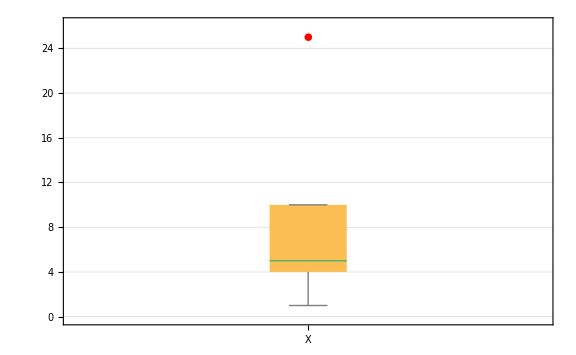

```mathematica
BoxWhiskerChart[data//N,
{"Outliers",{"Outliers",Style["●",Red,FontSlant->Plain]},{"FarOutliers","○"},{"MedianMarker",RGBColor[0.28026441037696703, 0.715, 0.4292089322474965]}},
Method->{"BoxRange"->(Flatten[{Min[#],quantile[#,{0.25,0.5,0.75}],Max[#]}]&)},
PlotTheme->{"myTheme","Detailed"},
ChartLabels->{"X"},
ChartStyle->Directive[Thick],
FrameTicksStyle->{Directive[FontSlant->Plain,FontSize->16],Automatic}
]
```

What do the numbers show us?

1: 75 % quantile

2: median (50 % quantile)

3: 25 % quantile

6: interquartile range

Lower whisker (more information)

```mathematica
Min[Cases[data,x_/;x≥quantile[data,0.25]-1.5*IQR]]
```

1

Upper whisker

```mathematica
Max[Cases[data,x_/;x≤quantile[data,0.75]+1.5*IQR]]
```

10

The sign of the skewness g can be inferred from the plot by looking at the median value (green line). If it is below the centre line, the data is right-skewed (like here).

## Part 3: Quartile Skewness

The quartile skewness is bounded to [-1;1]

Only the sign matters (like for the normal skewness)

[-1;0[ left-skewed

0 not-skewed at all (symmetric)

]0;1] right-skewed

We can think of the median value sliding between (x̃)_0.25 and (x̃)_0.75, thus leaving

a=-1 if (x̃)_0.75=(x̃)_0.5

b=1 if (x̃)_0.25=(x̃)_0.5

To achieve g_Q=-1, we must ensure that the 75 % quantile is the same as the median, e.g.

```mathematica
QuartileSkewness[{1,2,2}]
```

-1

Analog for +1, the 25 % quantile and the median must be identical, e.g.

```mathematica
QuartileSkewness[{2,1,1}]
```

1

## Part 4: Cartoons

Just some thoughts on the cartoons:

Mean: strong influence of extreme values

Median: says nothing about the range of the data or how it is distributed

Mode: the most common value may be totally meaningless if there are lots of other values. Also, it does not say how often a value occurs. Does not take into account the skewness or range of the data.

Range: no information how often a value occurs

Correlation coefficient: strong influence of outliers (quadratic!)

Variance: influence of outliers, different distributions can lead to the same variance